## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataPh=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/6sem/6112/tables/ph.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataPh//TableForm
```

n | phi
1. | 1600.
2. | 1800.
3. | 1915.
4. | 2000.
8. | 2250.
14. | 2500.
20. | 2690.
30. | 3000.
33.5 | 3100.
25. | 2840.
40. | 3300.
47. | 3500.

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[30.6921-0.0249279 x-7.36413×10^-6 x^2+9.30636×10^-9 x^3-1.36878×10^-12 x^4]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 30.6921 | 35.2624 | 0.870393 | 0.412936
x | -0.0249279 | 0.0591805 | -0.421218 | 0.686228
x^2 | -7.36413×10^-6 | 0.0000364227 | -0.202185 | 0.845523
x^3 | 9.30636×10^-9 | 9.74603×10^-9 | 0.954887 | 0.371439
x^4 | -1.36878×10^-12 | 9.57601×10^-13 | -1.42939 | 0.195965

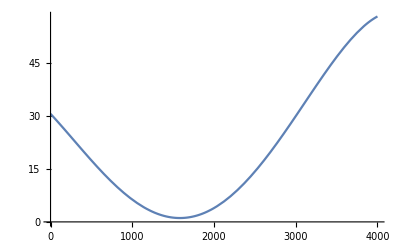

```mathematica
forFitPh=dataPh⟦2;;,{2,1}⟧;
fitPh=LinearModelFit[forFitPh,{1,x,x^2,x^3,x^4},x]
fitPh@"ParameterTable"
Plot[fitPh["Function"]@x, {x, 0, 4000}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

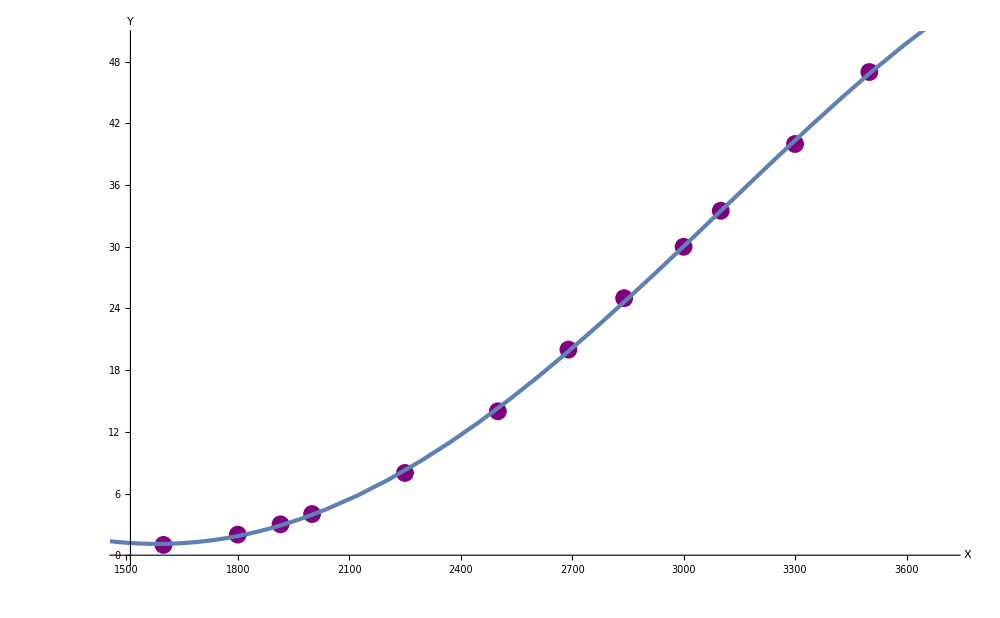

```mathematica
Show[ListPlot[dataPh⟦2;;,{2,1}⟧,
GridLines->{grids@200,grids@2.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{1500,3700},{0,50}}], 
Plot[fitPh["Function"]@x,{x,0,4000}, PlotStyle->Thickness@0.003]]
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataCdS=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/6sem/6112/tables/cds.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataCdS//TableForm
```

фи | U, mV | N |  | 
3200. | 5. | 37. | 0.135362 | 8866.78
1500. | 10. | 1. | 8.26123 | 4989.86
1565. | 11.8 | 1. | 10.686 | 5060.57
1630. | 16.5 | 1. | 14.5377 | 5133.84
1695. | 36.2 | 1. | 27.7693 | 5209.2
1760. | 56.7 | 2. | 35.2078 | 5286.32
1825. | 66. | 2. | 32.1128 | 5365.05
1890. | 70.3 | 3. | 26.657 | 5445.4
1955. | 71.8 | 3. | 21.4017 | 5527.52
2020. | 74.3 | 4. | 17.6643 | 5611.73
2085. | 75.5 | 5. | 14.5508 | 5698.52
2150. | 76.3 | 6. | 12.1128 | 5788.53
2215. | 78. | 8. | 10.3535 | 5882.57
2280. | 79.9 | 9. | 8.98964 | 5981.57
2345. | 81.3 | 10. | 7.84959 | 6086.68
2410. | 84.3 | 12. | 7.06281 | 6199.17
2475. | 95. | 14. | 6.9763 | 6320.48
2540. | 110.4 | 15. | 7.17078 | 6452.2
2605. | 127.7 | 17. | 7.39719 | 6596.1
2670. | 141.5 | 19. | 7.36512 | 6754.09
2735. | 149.7 | 21. | 7.05004 | 6928.26
2800. | 149.3 | 23. | 6.40236 | 7120.83
2770. | 155. | 22. | 6.93524 | 7029.51
2865. | 129.5 | 25. | 5.08654 | 7334.2
2930. | 88.5 | 28. | 3.20151 | 7570.94
2900. | 104.7 | 27. | 3.93159 | 7458.61
2995. | 83.8 | 30. | 2.80641 | 7833.76
3060. | 66.2 | 32. | 2.06237 | 8125.53
3125. | 16.1 | 34. | 0.468737 | 8449.28
3090. | 31.3 | 33. | 0.944582 | 8270.79
3190. | 5. | 37. | 0.136636 | 8808.23

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFitPh=dataPh⟦2;;,{2,1}⟧;
fitPh=LinearModelFit[forFitPh,{1,x,x^2,x^3,x^4},x]
fitPh@"ParameterTable"
Plot[fitPh["Function"]@x, {x, 0, 4000}]
```

FittedModel[30.6921-0.0249279 x-7.36413×10^-6 x^2+9.30636×10^-9 x^3-1.36878×10^-12 x^4]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 30.6921 | 35.2624 | 0.870393 | 0.412936
x | -0.0249279 | 0.0591805 | -0.421218 | 0.686228
x^2 | -7.36413×10^-6 | 0.0000364227 | -0.202185 | 0.845523
x^3 | 9.30636×10^-9 | 9.74603×10^-9 | 0.954887 | 0.371439
x^4 | -1.36878×10^-12 | 9.57601×10^-13 | -1.42939 | 0.195965

-Graphics-

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

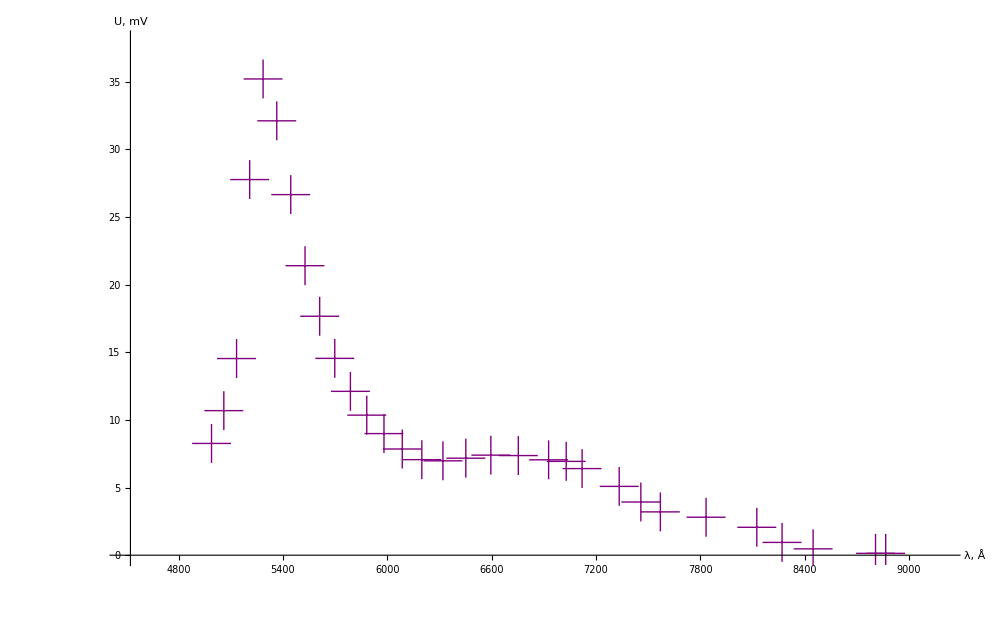

```mathematica
Show[ListPlot[dataCdS⟦2;;,{5,4}⟧,
GridLines->{grids@100,grids@2.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"λ, Å","U, mV"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
PlotMarkers->{"+", 40},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{4500,9200},{0,38}}], 
Plot[fitPh["Function"]@x,{x,0,1}, PlotStyle->Thickness@0.003]]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,4,5,5}⟧,
GridLines->{grids@0.5,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,6.9},{0,15}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataCdSl=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/6sem/6112/tables/cdsl.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataCdSl//TableForm
```

фи | U, mV |  |  | 
3180. | 15. | 36. | 0.413808 | 8750.58
3145. | 67. | 35. | 1.91213 | 8555.83
3160. | 41.7 | 36. | 1.17273 | 8637.98
3110. | 78.7 | 34. | 2.32644 | 8371.57
3075. | 84.1 | 33. | 2.57837 | 8197.29
3040. | 112. | 31. | 3.56591 | 8032.49
3005. | 136.4 | 30. | 4.51604 | 7876.69
2970. | 152. | 29. | 5.24061 | 7729.41
2935. | 161. | 28. | 5.78873 | 7590.2
2900. | 162. | 27. | 6.08326 | 7458.61
2915. | 163. | 27. | 6.00681 | 7514.1
2865. | 156.9 | 25. | 6.16276 | 7334.2
2830. | 141. | 24. | 5.80223 | 7216.57
2795. | 117. | 23. | 5.05246 | 7105.31
2760. | 95.5 | 22. | 4.33519 | 7000.02
2725. | 88.2 | 21. | 4.21636 | 6900.32
2690. | 87.6 | 20. | 4.41824 | 6805.86
2655. | 81. | 19. | 4.3187 | 6716.28
2620. | 55.2 | 18. | 3.11757 | 6631.24
2585. | 30.2 | 17. | 1.81059 | 6550.42
2550. | 21.9 | 16. | 1.39691 | 6473.5
2515. | 19.9 | 15. | 1.35366 | 6400.2
2480. | 18.5 | 14. | 1.34536 | 6330.22
2445. | 16.5 | 13. | 1.28616 | 6263.3
2410. | 14.7 | 12. | 1.23159 | 6199.17

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFitPh=dataPh⟦2;;,{2,1}⟧;
fitPh=LinearModelFit[forFitPh,{1,x,x^2,x^3,x^4},x]
fitPh@"ParameterTable"
Plot[fitPh["Function"]@x, {x, 0, 4000}]
```

FittedModel[30.6921-0.0249279 x-7.36413×10^-6 x^2+9.30636×10^-9 x^3-1.36878×10^-12 x^4]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 30.6921 | 35.2624 | 0.870393 | 0.412936
x | -0.0249279 | 0.0591805 | -0.421218 | 0.686228
x^2 | -7.36413×10^-6 | 0.0000364227 | -0.202185 | 0.845523
x^3 | 9.30636×10^-9 | 9.74603×10^-9 | 0.954887 | 0.371439
x^4 | -1.36878×10^-12 | 9.57601×10^-13 | -1.42939 | 0.195965

-Graphics-

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

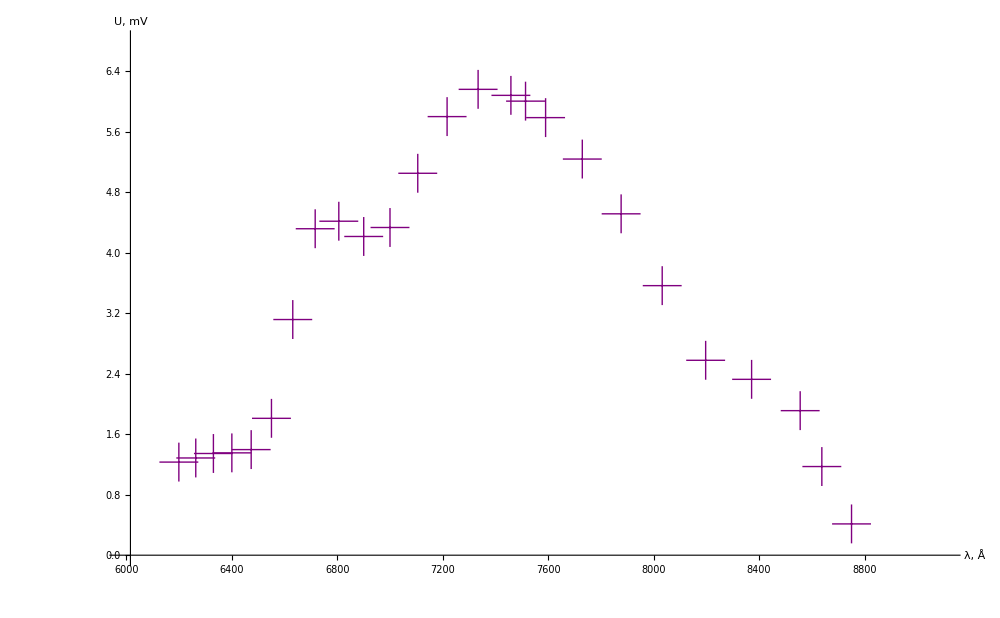

```mathematica
Show[ListPlot[dataCdSl⟦2;;,{5,4}⟧,
GridLines->{grids@100,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"λ, Å","U, mV"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
PlotMarkers->{"+", 40},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{6000,9100},{0,6.8}}], 
Plot[fitPh["Function"]@x,{x,0,1}, PlotStyle->Thickness@0.003]]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,4,5,5}⟧,
GridLines->{grids@0.5,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,6.9},{0,15}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```

## Построение одного графика

### Импорт табличных данных

```mathematica
datal=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/6sem/6112/tables/l.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
datal//TableForm
```

lambda | phi
4600. | 1600.
4700. | 1690.
4900. | 1850.
5090. | 2000.
5500. | 2300.
5700. | 2415.
5880. | 2500.
6100. | 2600.
6200. | 2650.
6500. | 2765.
6800. | 2850.
7350. | 3000.
7800. | 3100.
8100. | 3150.

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[7091.69-8.02654 x+0.00736116 x^2-2.66988×10^-6 x^3+3.72585×10^-10 x^4]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 7091.69 | 3424.91 | 2.07062 | 0.0682952
x | -8.02654 | 6.04913 | -1.32689 | 0.217222
x^2 | 0.00736116 | 0.0039386 | 1.86898 | 0.094452
x^3 | -2.66988×10^-6 | 1.12129×10^-6 | -2.38109 | 0.0411543
x^4 | 3.72585×10^-10 | 1.17856×10^-10 | 3.16135 | 0.0115252

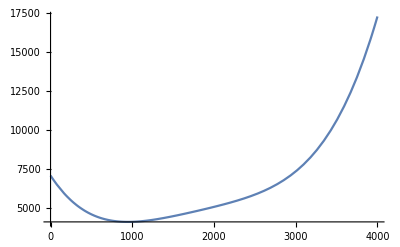

```mathematica
forFitl=datal⟦2;;,{2,1}⟧;
fitl=LinearModelFit[forFitl,{1,x,x^2,x^3,x^4},x]
fitl@"ParameterTable"
Plot[fitl["Function"]@x, {x, 0, 4000}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

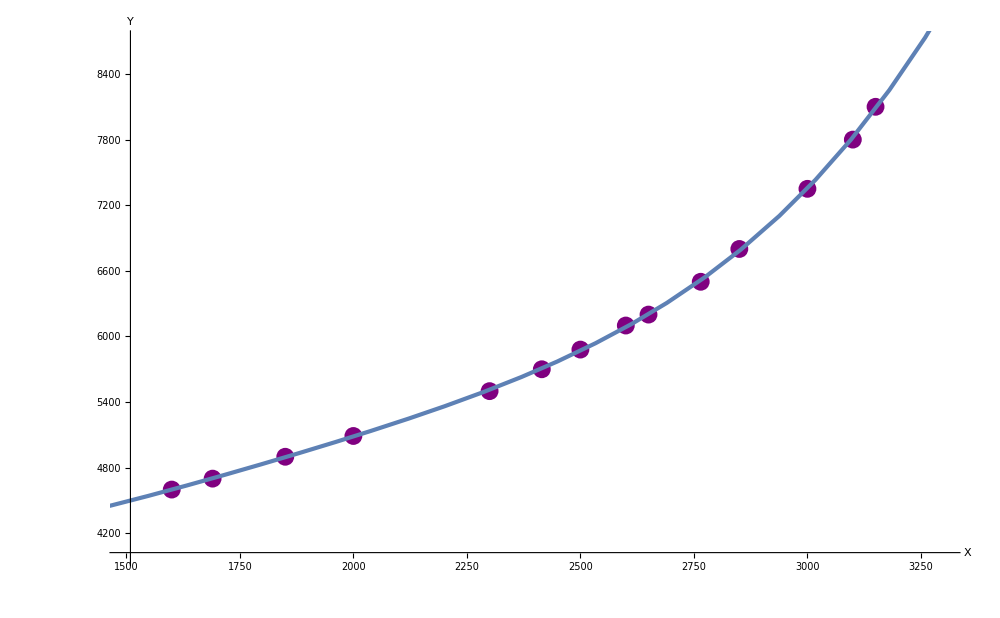

```mathematica
Show[ListPlot[datal⟦2;;,{2,1}⟧,
GridLines->{grids@100,grids@100},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{1500,3300},{4000,8700}}], 
Plot[fitl["Function"]@x,{x,0,4000}, PlotStyle->Thickness@0.003]]
```

```mathematica
f=-4.09137*(10)^1+7.12905*x-3.75638*10^-3*x^2+7.92467*10^-7*x^3
```

-40.9137+7.12905 x-0.00375638 x^2+7.92467×10^-7 x^3

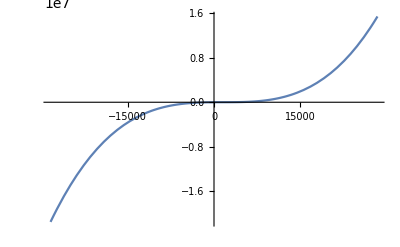

```mathematica
Plot[f,{x,-28440.65431115744,28440.65431115744}]
```

```mathematica
FittedModel[7091.687608138622-8.026537872495995 x+0.007361158004167876 x^2-2.669882123881404*^-6 x^3+3.725850289611817*^-10 x^4]
```

```mathematica
fitl["Function"]@x
```

7091.69-8.02654 x+0.00736116 x^2-2.66988×10^-6 x^3+3.72585×10^-10 x^4

```mathematica
-3.75638e-03
```

-3-3.75638 e

## Построение одного графика

### Импорт табличных данных

```mathematica
datad=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/6sem/6112/tables/d.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
datad//TableForm
```

# | фи | U, mV | N |  |  | фи | U, mV |  |  | 
1. | 3200. | 5. | 37. | 0.1 | 8867. | 3180. | 15. | 36. | 0.4 | 8751.
2. | 1500. | 10. | 1. | 8.3 | 4990. | 3145. | 67. | 35. | 1.9 | 8556.
3. | 1565. | 11.8 | 1. | 10.7 | 5061. | 3160. | 41.7 | 36. | 1.2 | 8638.
4. | 1630. | 16.5 | 1. | 14.5 | 5134. | 3110. | 78.7 | 34. | 2.3 | 8372.
5. | 1695. | 36.2 | 1. | 27.8 | 5209. | 3075. | 84.1 | 33. | 2.6 | 8197.
6. | 1760. | 56.7 | 2. | 35.2 | 5286. | 3040. | 112. | 31. | 3.6 | 8032.
7. | 1825. | 66. | 2. | 32.1 | 5365. | 3005. | 136.4 | 30. | 4.5 | 7877.
8. | 1890. | 70.3 | 3. | 26.7 | 5445. | 2970. | 152. | 29. | 5.2 | 7729.
9. | 1955. | 71.8 | 3. | 21.4 | 5528. | 2935. | 161. | 28. | 5.8 | 7590.
10. | 2020. | 74.3 | 4. | 17.7 | 5612. | 2900. | 162. | 27. | 6.1 | 7459.
11. | 2085. | 75.5 | 5. | 14.6 | 5699. | 2915. | 163. | 27. | 6. | 7514.
12. | 2150. | 76.3 | 6. | 12.1 | 5789. | 2865. | 156.9 | 25. | 6.2 | 7334.
13. | 2215. | 78. | 8. | 10.4 | 5883. | 2830. | 141. | 24. | 5.8 | 7217.
14. | 2280. | 79.9 | 9. | 9. | 5982. | 2795. | 117. | 23. | 5.1 | 7105.
15. | 2345. | 81.3 | 10. | 7.8 | 6087. | 2760. | 95.5 | 22. | 4.3 | 7000.
16. | 2410. | 84.3 | 12. | 7.1 | 6199. | 2725. | 88.2 | 21. | 4.2 | 6900.
17. | 2475. | 95. | 14. | 7. | 6320. | 2690. | 87.6 | 20. | 4.4 | 6806.
18. | 2540. | 110.4 | 15. | 7.2 | 6452. | 2655. | 81. | 19. | 4.3 | 6716.
19. | 2605. | 127.7 | 17. | 7.4 | 6596. | 2620. | 55.2 | 18. | 3.1 | 6631.
20. | 2670. | 141.5 | 19. | 7.4 | 6754. | 2585. | 30.2 | 17. | 1.8 | 6550.
21. | 2735. | 149.7 | 21. | 7.1 | 6928. | 2550. | 21.9 | 16. | 1.4 | 6474.
22. | 2800. | 149.3 | 23. | 6.4 | 7121. | 2515. | 19.9 | 15. | 1.4 | 6400.
23. | 2770. | 155. | 22. | 6.9 | 7030. | 2480. | 18.5 | 14. | 1.3 | 6330.
24. | 2865. | 129.5 | 25. | 5.1 | 7334. | 2445. | 16.5 | 13. | 1.3 | 6263.
25. | 2930. | 88.5 | 28. | 3.2 | 7571. | 2410. | 14.7 | 12. | 1.2 | 6199.
26. | 2900. | 104.7 | 27. | 3.9 | 7459. |  |  |  |  | 
27. | 2995. | 83.8 | 30. | 2.8 | 7834. |  |  |  |  | 
28. | 3060. | 66.2 | 32. | 2.1 | 8126. |  |  |  |  | 
29. | 3125. | 16.1 | 34. | 0.5 | 8449. |  |  |  |  | 
30. | 3090. | 31.3 | 33. | 0.9 | 8271. |  |  |  |  | 
31. | 3190. | 5. | 37. | 0.1 | 8808. |  |  |  |  |

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,4,5,5}⟧,
GridLines->{grids@0.5,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,6.9},{0,15}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,datad,{{2;;,All}}];
forTeX//TeXForm
```

\left(
\begin{array}{ccccccccccc}
 \# & \unicode{0444}\unicode{0438} & \text{U, mV} & \text{N} & \text{} & \text{} & \unicode{0444}\unicode{0438} & \text{U, mV} & \text{} & \text{} & \text{} \\
 1 & 3200 & 5 & 37 & 0.1 & 8867 & 3180 & 15 & 36 & 0.4 & 8751 \\
 2 & 1500 & 10 & 1 & 8.3 & 4990 & 3145 & 67 & 35 & 1.9 & 8556 \\
 3 & 1565 & 11.8 & 1 & 10.7 & 5061 & 3160 & 41.7 & 36 & 1.2 & 8638 \\
 4 & 1630 & 16.5 & 1 & 14.5 & 5134 & 3110 & 78.7 & 34 & 2.3 & 8372 \\
 5 & 1695 & 36.2 & 1 & 27.8 & 5209 & 3075 & 84.1 & 33 & 2.6 & 8197 \\
 6 & 1760 & 56.7 & 2 & 35.2 & 5286 & 3040 & 112 & 31 & 3.6 & 8032 \\
 7 & 1825 & 66 & 2 & 32.1 & 5365 & 3005 & 136.4 & 30 & 4.5 & 7877 \\
 8 & 1890 & 70.3 & 3 & 26.7 & 5445 & 2970 & 152 & 29 & 5.2 & 7729 \\
 9 & 1955 & 71.8 & 3 & 21.4 & 5528 & 2935 & 161 & 28 & 5.8 & 7590 \\
 10 & 2020 & 74.3 & 4 & 17.7 & 5612 & 2900 & 162 & 27 & 6.1 & 7459 \\
 11 & 2085 & 75.5 & 5 & 14.6 & 5699 & 2915 & 163 & 27 & 6 & 7514 \\
 12 & 2150 & 76.3 & 6 & 12.1 & 5789 & 2865 & 156.9 & 25 & 6.2 & 7334 \\
 13 & 2215 & 78 & 8 & 10.4 & 5883 & 2830 & 141 & 24 & 5.8 & 7217 \\
 14 & 2280 & 79.9 & 9 & 9 & 5982 & 2795 & 117 & 23 & 5.1 & 7105 \\
 15 & 2345 & 81.3 & 10 & 7.8 & 6087 & 2760 & 95.5 & 22 & 4.3 & 7000 \\
 16 & 2410 & 84.3 & 12 & 7.1 & 6199 & 2725 & 88.2 & 21 & 4.2 & 6900 \\
 17 & 2475 & 95 & 14 & 7 & 6320 & 2690 & 87.6 & 20 & 4.4 & 6806 \\
 18 & 2540 & 110.4 & 15 & 7.2 & 6452 & 2655 & 81 & 19 & 4.3 & 6716 \\
 19 & 2605 & 127.7 & 17 & 7.4 & 6596 & 2620 & 55.2 & 18 & 3.1 & 6631 \\
 20 & 2670 & 141.5 & 19 & 7.4 & 6754 & 2585 & 30.2 & 17 & 1.8 & 6550 \\
 21 & 2735 & 149.7 & 21 & 7.1 & 6928 & 2550 & 21.9 & 16 & 1.4 & 6474 \\
 22 & 2800 & 149.3 & 23 & 6.4 & 7121 & 2515 & 19.9 & 15 & 1.4 & 6400 \\
 23 & 2770 & 155 & 22 & 6.9 & 7030 & 2480 & 18.5 & 14 & 1.3 & 6330 \\
 24 & 2865 & 129.5 & 25 & 5.1 & 7334 & 2445 & 16.5 & 13 & 1.3 & 6263 \\
 25 & 2930 & 88.5 & 28 & 3.2 & 7571 & 2410 & 14.7 & 12 & 1.2 & 6199 \\
 26 & 2900 & 104.7 & 27 & 3.9 & 7459 & \text{} & \text{} & \text{} & \text{} & \text{} \\
 27 & 2995 & 83.8 & 30 & 2.8 & 7834 & \text{} & \text{} & \text{} & \text{} & \text{} \\
 28 & 3060 & 66.2 & 32 & 2.1 & 8126 & \text{} & \text{} & \text{} & \text{} & \text{} \\
 29 & 3125 & 16.1 & 34 & 0.5 & 8449 & \text{} & \text{} & \text{} & \text{} & \text{} \\
 30 & 3090 & 31.3 & 33 & 0.9 & 8271 & \text{} & \text{} & \text{} & \text{} & \text{} \\
 31 & 3190 & 5 & 37 & 0.1 & 8808 & \text{} & \text{} & \text{} & \text{} & \text{} \\
\end{array}
\right)